# IndependentComponentAnalysis

Decomposes a matrix into Independent Component Analysis matrix factors.

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
Clear[IndependentComponentAnalysis];

IndependentComponentAnalysis::nargs="A numeric matrix and a positive integer are expected as a first and a second argument respectively.";
IndependentComponentAnalysis::nomat="A numeric matrix is expected as a first argument.";
IndependentComponentAnalysis::noint="A positive integer no greater than the number of columns of the matrix is expected as a second argument.";
IndependentComponentAnalysis::unmat="The un-mixing matrix option value should be Automatic or a square matrix corresponding to the number of components.";
IndependentComponentAnalysis::nnum="Non-numerical internal result was obtained."

FastICA::nomat="A matrix is expected as a first argument.";
FastICA::noint="A positive integer no greater than the number of columns of the matrix is expected as a second argument.";
FastICA::unmat="The un-mixing matrix option value should be Automatic or a square matrix corresponding to the number of components.";

Options[IndependentComponentAnalysis]={MaxSteps->200,PrecisionGoal->6,"NonGaussianityFunction"->Automatic,"NegEntropyFactor"->1,"InitialUnmixingMartix"->Automatic,"RowNorm"->False};

IndependentComponentAnalysis[X_,k_,opts:OptionsPattern[]]:=
Block[{nonGaussFunc,alpha,rowNormQ,unmixMatSpec,maxSteps,pgoal,res},

If[!MatrixQ[X,NumericQ],
Message[IndependentComponentAnalysis::nomat];
Return[$Failed]
];

If[!IntegerQ[k]||!(1<=k<=Dimensions[X][[2]]),
Message[IndependentComponentAnalysis::noint];
Return[$Failed]
];

res=FastICA[X,k,"RFastICAResult"->False,opts];

If[AssociationQ[res],{res["S"],res["A"]},res]
];

IndependentComponentAnalysis[___]:=
Block[{},
Message[IndependentComponentAnalysis::nargs];
Return[$Failed]
];
```

Non-numerical internal result was obtained.

```mathematica
Clear[FastICA];

Options[FastICA]={"NonGaussianityFunction"->Automatic,"NegEntropyFactor"->1,"InitialUnmixingMartix"->Automatic,"RowNorm"->False,MaxSteps->200,PrecisionGoal->6,"RFastICAResult"->True};

FastICA[X_?MatrixQ,k_Integer,opts:OptionsPattern[]]:=
Block[{nonGaussFunc,alpha,rowNormQ,unmixMatSpec,maxSteps,pgoal,n,m,ncomp=k,wInitMat,V,XU,XD,XV,XD1,K,X1,W,aMat,wMat,S,A},

nonGaussFunc=OptionValue[FastICA,"NonGaussianityFunction"];
alpha=OptionValue[FastICA,"NegEntropyFactor"];
rowNormQ=OptionValue[FastICA,"RowNorm"];
unmixMatSpec=OptionValue[FastICA,"InitialUnmixingMartix"];
maxSteps=OptionValue[FastICA,MaxSteps];
pgoal=OptionValue[FastICA,PrecisionGoal];

If[!MatrixQ[X],
Message[IndependentComponentAnalysis::nomat];
Return[$Failed]
];

If[!IntegerQ[ncomp]||!(1≤k<=Dimensions[X]⟦2⟧),
Message[IndependentComponentAnalysis::noint];
Return[$Failed]
];

If[TrueQ[nonGaussFunc===Automatic],
nonGaussFunc=Log[Cosh[#]]&;
];

Which[
TrueQ[unmixMatSpec===Automatic],
wInitMat=Partition[RandomVariate[NormalDistribution[],ncomp^2],ncomp],

TrueQ[MatrixQ[unmixMatSpec]&&Dimensions[unmixMatSpec]=={ncomp,ncomp}],
wInitMat=unmixMatSpec,

True,
Message[IndependentComponentAnalysis::unmat];
Return[$Failed]
];

{n,m}=Dimensions[X];

(*Centering*)
If[rowNormQ,
X1=Standardize[#,Mean,StandardDeviation]&/@Transpose[X],
X1=Standardize[#,Mean,1&]&/@Transpose[X]
];

If[TrueQ[Head[X]===SparseArray],
X1=SparseArray[X1]
];

(*Whitening*)
V=X1.Transpose[X1]/n;
{XU,XD,XV}=SingularValueDecomposition[V];
XD1=DiagonalMatrix[1/Sqrt[Map[If[#<10^-12,1,#]&,Diagonal[XD]]]];
K=XD1.Transpose[XU];
K=K[[1;;ncomp,All]];

If[TrueQ[Head[X]===SparseArray],
K=SparseArray[K]
];

(*X1=K.X1;*)
aMat=ICADeflation[K.X1,ncomp,wInitMat,nonGaussFunc,pgoal,alpha,maxSteps];
If[TrueQ[aMat===$Failed],
Return[$Failed]
];

If[TrueQ[Head[X]===SparseArray],aMat=SparseArray[aMat]];

K=Transpose[K];
aMat=Transpose[aMat];
X1=Transpose[X1];
wMat=K.aMat;
A=Transpose[wMat.Inverse[Transpose[wMat].wMat]];

If[OptionValue[FastICA,"RFastICAResult"],
S=X1.wMat;
AssociationThread[{"X","K","W","A","S"}->{X1,K,aMat,A,S}],
(*ELSE*)
S=X.wMat;
AssociationThread[{"K","W","A","S"}->{K,aMat,A,S}]
]
];
```

```mathematica
Clear[ICADeflation];
ICADeflation[X_?MatrixQ,ncomp_Integer,wInitMat_?MatrixQ,func_,pgoal_?NumberQ,alpha_?NumberQ,maxSteps_Integer]:=Block[{n,m,w,w1,W,g,gp,t,k,nStep=0,wx,gwx,gwxMat,xgwxMat,gpwx,v1,v2,wd},

{n,m}=Dimensions[X];
g=func';
gp=func'';

W=ConstantArray[0,{ncomp,ncomp}];

Do[w=wInitMat[[i,All]];
If[i>1,t=ConstantArray[0,Length[w]];
Do[
k=w.W[[j,All]];
t=t+k*W[[j,All]];
,{j,1,i-1}
];
w=w-t;
];

w=w/Norm[w];
wd=1000;

While[wd>10^-pgoal&&nStep<maxSteps,
nStep++;
wx=w.X;
gwx=g[alpha*wx];
If[!VectorQ[gwx,NumericQ],
Message[IndependentComponentAnalysis::nnum];
Return[$Failed]
];
gwxMat=Table[gwx,{ncomp}];
xgwxMat=X*gwxMat;
v1=Mean/@xgwxMat;
gpwx=alpha*g[alpha*wx];
v2=Mean[gpwx]*w;
w1=v1-v2;
If[i>1,t=ConstantArray[0,Length[w1]];
Do[k=w1.W[[j,All]];
t=t+k*W[[j,All]];,{j,1,i-1}];
w1=w1-t;
];
w1=w1/Norm[w1];
wd=Abs[Abs[w.w1]-1];
w=w1;
];(*While*)

W[[i,All]]=w;
,{i,1,ncomp}
];(*Do*)

W
];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

IndependentComponentAnalysis[mat,k]

decomposes the matrix mat into k components.

IndependentComponentAnalysis[mat,k,opts]

decomposes the matrix mat into k components using the options opts.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

The Independent Component Analysis (ICA) is a matrix factorization method that utilizes Gram–Schmidt orthogonolization by considering two vectors (two signals) to be orthogonal if their difference is Gausian white noise.

The argument matrix can be square or rectangular.

The columns of the argement matrix are interpreted as signals.

Here are the options taken by IndependentComponentAnalysis:

"InitialUnmixingMartix" | Automatic | Initial un-mixing matrix.
"NegEntropyFactor" | 1 | Negative entropy factor.
"NonGaussianityFunction" | Automatic | Non-Gaussianity measure function.
"RowNorm" | False | Should the matrix rows be normalized at each step or not?
MaxSteps | 200 | Maximum steps of the ICA interation process.
PrecisionGoal | 6 | Precision goal.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Here is a random integer matrix:

```mathematica
SeedRandom[7]
mat=RandomInteger[10,{4,3}];
MatrixForm[mat]
```

(4 | 7 | 4
10 | 8 | 8
5 | 3 | 4
5 | 4 | 5)

Here are the Independent Component Analysis matrix factors:

```mathematica
{A,S}=IndependentComponentAnalysis[mat,3];
Row[{MatrixForm[A],MatrixForm[S]}]
```

(-2.86018 | -1.81129 | -2.56681
-2.86065 | 0.186103 | -4.56941
-0.85907 | 0.1876 | -2.571
-0.861758 | -1.815 | -4.56839)(-1.00035 | -2.00039 | -0.750573
1.4986 | 0.000457809 | 0.748786
-1.50116 | -0.49842 | -1.25038)

Here is the matrix product of the obtained factors:

```mathematica
MatrixForm[A.S]
```

(4. | 7. | 4.
10. | 8. | 8.
5. | 3. | 4.
5. | 4. | 5.)

### Scope

Here is a random matrix that has its first three columns with much large magnitudes than the rest:

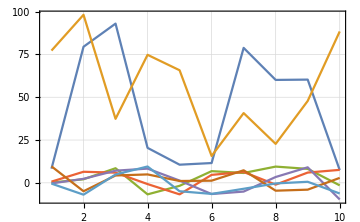

```mathematica
SeedRandom[232];
mat=RandomReal[{10,100},{10,2}];
mat2=RandomReal[{-10,10},{10,7}];
mat=ArrayPad[mat,{{0,0},{0,5}}]+mat2;
ListLinePlot[Transpose[mat],PlotRange->All,ImageSize->Medium,PlotTheme->"Detailed"]
```

Here is a ICA matrix factors computation:

```mathematica
SeedRandom[22];
{A,S}=IndependentComponentAnalysis[mat,3,MaxSteps->100,PrecisionGoal->8];
```

Here is the relative error of the approximation by the obtained matrix factorization:

```mathematica
Norm[mat-A.S]/Norm[mat]
```

0.103854

Here is the relative error for the first three columns:

```mathematica
Norm[mat⟦All,1;;3⟧-(A.S)⟦All,1;;3⟧]/Norm[mat⟦All,1;;3⟧]
```

0.0852882

Here are comparison plots:

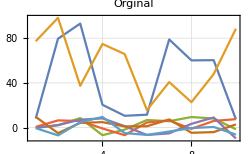
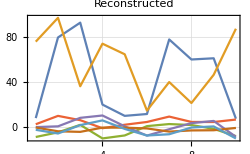

```mathematica
Block[{opts={PlotRange->All,ImageSize->250,PlotTheme->"Detailed"}},
Row[{ListLinePlot[Transpose[mat],opts,PlotLabel->"Orginal"],ListLinePlot[Transpose[A.S],opts,PlotLabel->"Reconstructed"]}]
]
```

### Options

#### “InitialUnmixingMartix”

Using the option “InitialUnmixingMartix” we can influence the results by providing initial un-mixing matrix for ICA’s iteration process.

Here we compute ICA with different initial un-mixing matrices:

```mathematica
k=3;
SeedRandom[8];
res=Association[
MapThread[Row[{#2,":",Spacer[2],If[MatrixQ[#],MatrixForm[#1],ToString[#1]]}]->IndependentComponentAnalysis[mat,k,"InitialUnmixingMartix"->#1]&,{{Automatic,Automatic,RandomVariate[NormalDistribution[1,10],{k,k}],SingularValueDecomposition[mat,k]⟦2⟧},Range[4]}]];
```

Here we plot the results:

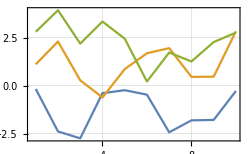
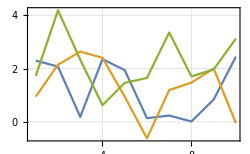
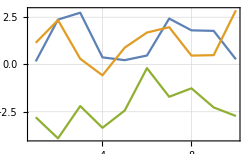
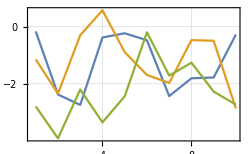
1:Automatic | 2:Automatic | 3:(-29.5756 | 3.7515 | 5.1016
18.4862 | 2.24943 | 5.51222
-11.6546 | 1.44047 | 2.60197) | 4:(240.005 | 0. | 0.
0. | 107.593 | 0.
0. | 0. | 24.0641)
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Transpose@KeyValueMap[{#1,ListLinePlot[Transpose[#2⟦1⟧],PlotRange->All,ImageSize->250,PlotTheme->"Detailed"]}&,res],Alignment->{Center,Left}]
```

Note the similarities and differences in the results.

#### “NegEntropyFactor”

The negative entropy factor is specified with the option “NegEntropyFactor”. The negative entropy factor controls how aggressively ICA learns from “landscape” produced by the non-Gaussianity measure function. (Specified with “NonGaussianityFunction”.)

#### "NonGaussianityFunction"

ICA is essentially a Gram–Schmidt process that considers two signals to be orthogonal if their difference is Gaussian noise.

Here we compute ICA with different non-Gaussianity measure functions:

```mathematica
res=Association[
#->BlockRandom[
SeedRandom[22];
IndependentComponentAnalysis[mat,3,"NonGaussianityFunction"->#,MaxSteps->2]
]&/@{Log[Cosh[#]]&,-Exp[-#^2/2]&,(Log[Cosh[1.2#]]/1.2&)}];
```

Here we plot the results:

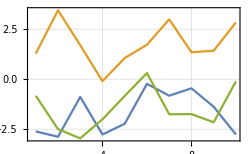
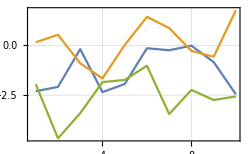
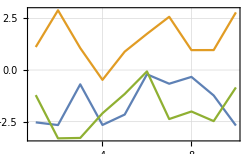
Log[Cosh[x]] | -ⅇ^(-x^2/2) | 0.833333 Log[Cosh[1.2 x]]
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Transpose@KeyValueMap[{#1[x],ListLinePlot[Transpose[#2⟦1⟧],PlotRange->All,ImageSize->250,PlotTheme->"Detailed"]}&,res],Alignment->{Center,Left}]
```

Note that we used a small number of steps in order to obtain similar but different results. Using a sufficiently large number of steps, say, 20, we get almost the same results (with the matrix mat.)

#### MaxSteps

Specifies the maximum steps of the ICA iteration process.

#### PrecisionGoal

Specifies the precision goal of the ICA iteration process.

### Applications

#### Blind signal separation

Here are signal generating functions:

```mathematica
Clear[s1,s2,s3]
s1[t_]:=Sin[600 π t/10000+6*Cos[120 π t/10000]]+1.2
s2[t_]:=Sin[π t/10]+1.2
s3[t_?NumericQ]:=(((QuotientRemainder[t,23][[2]]-11)/9)^5+2.8)/2+0.2
```

Here is a mixing matrix:

```mathematica
A={{0.44,0.2,0.31},{0.45,0.8,0.23},{0.12,0.32,0.71}};
```

A matrix of the signals:

```mathematica
nSize=600;
S=Table[{s1[t],s2[t],s3[t]},{t,0,nSize,0.5}];
Dimensions[S]
```

{1201,3}

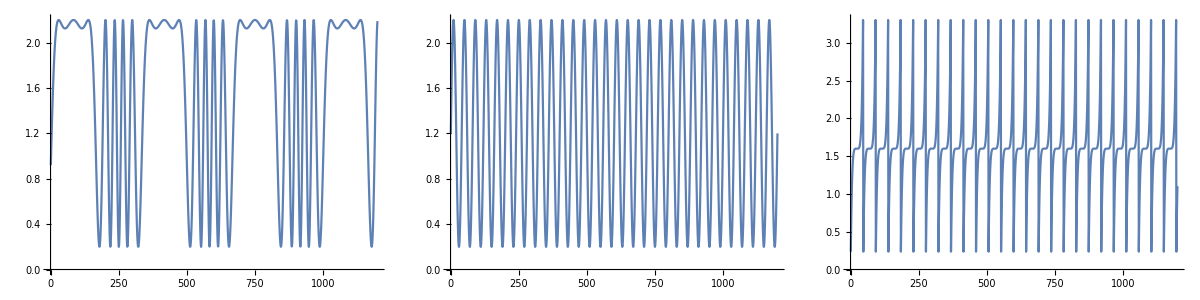

```mathematica
Grid[{Map[ListLinePlot[#,PlotRange->All,ImageSize->250]&,Transpose@S]}]
```

Mixed signals matrix:

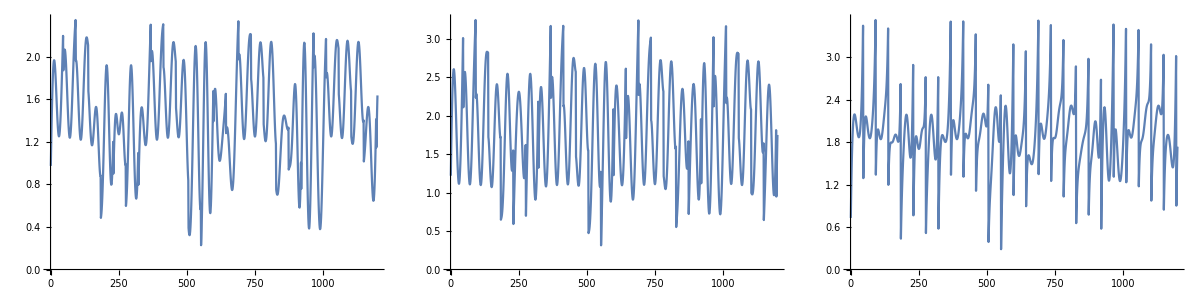

```mathematica
M=S.A;
Grid[{Map[ListLinePlot[#,PlotRange->All,ImageSize->250]&,Transpose@M]}]
```

ICA decomposition:

```mathematica
{A,S}=IndependentComponentAnalysis[M,3];
```

Approximation norm:

```mathematica
Norm[M-A.S]
```

4.75931×10^-14

Visualize ICA identified source signals:

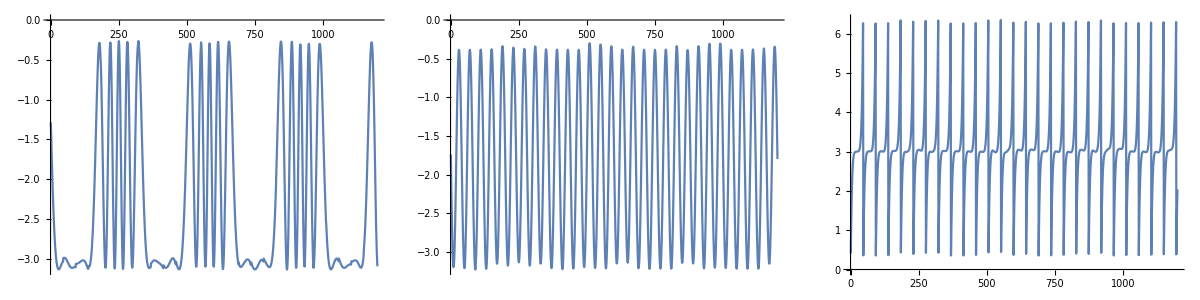

```mathematica
Grid[{Map[ListLinePlot[#,PlotRange->All,ImageSize->250]&,Transpose[A]]}]
```

### Properties and Relations

The function IndependentComponentAnalysis uses SingularValueDecomposition internally.

### Possible Issues

#### Multiple iterations

For some data at least several executions are required in order to get components that provide satisfactory interpretation.

#### Outliers presence sensitivity

The ICA computations can be sensitive to the presence of outliers.

Here we add a small number of outliers to the original mixed signals:

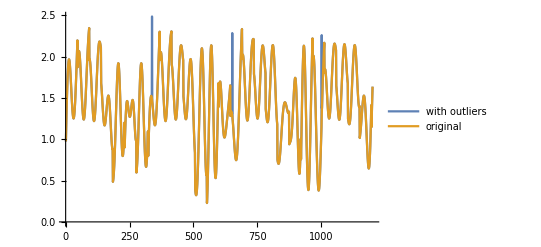
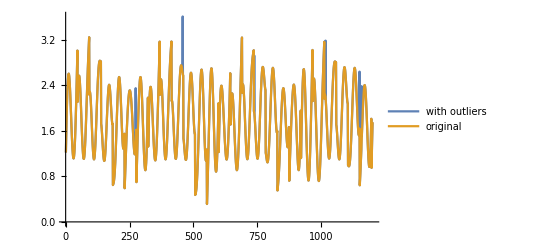
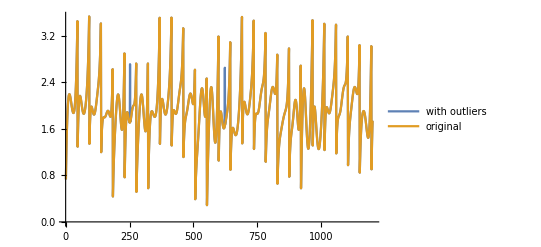

```mathematica
M1=M+RandomChoice[{0.005,0.995}->{1,0},Dimensions[M]];
MapThread[ListLinePlot[{##},PlotLegends->{"with outliers","original"}]&,{Transpose[M1],Transpose[M]}]
```

Here we apply ICA to the new mixed signals:

```mathematica
{A,S}=IndependentComponentAnalysis[M1,3];
```

We see that the found components are not that good compared to the components found over original mixed signals data:

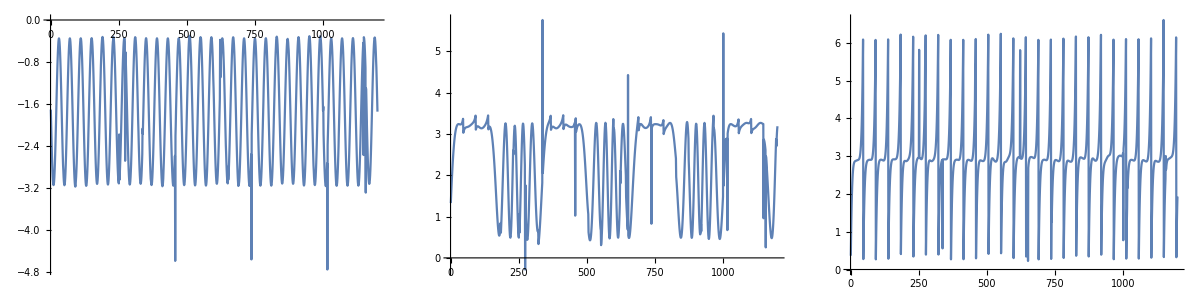

```mathematica
Grid[{Map[ListLinePlot[#,PlotRange->All,ImageSize->250]&,Transpose[A]]}]
```

### Neat Examples

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Anton Antonov

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Independent Component Analysis

Dimension reduction

Gram–Schmidt process

Non-Gaussianity

Gaussian noise

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

SingularValueDecomposition

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

A. Hyvarinen and E. Oja (2000) Independent Component Analysis: Algorithms and Applications, Neural Networks, 13(4-5):411-430.

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

https://cran.r-project.org/web/packages/fastICA/index.html

https://mathematicaforprediction.wordpress.com/2016/05/23/independent-component-analysis-for-multidimensional-signals/

https://github.com/antononcube/MathematicaForPrediction/blob/master/IndependentComponentAnalysis.m

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

#### Data

```mathematica
SeedRandom[443]
mat10by3=RandomReal[{-100,100},{10,3}];
mat10by10=RandomReal[{-100,100},{10,10}];
mat3by10=RandomReal[{-100,100},{3,10}];
```

#### These should pass

```mathematica
res=IndependentComponentAnalysis[mat10by3,2];
ListQ[res]&&Length[res]==2&&Apply[And,MatrixQ[#,NumberQ]&/@res]
```

True

```mathematica
Norm[mat10by3-res⟦1⟧.res⟦2⟧]/Norm[mat3by10]<10^(-8)
```

False

```mathematica
res=IndependentComponentAnalysis[mat10by3,3];
ListQ[res]&&Length[res]==2&&Apply[And,MatrixQ[#,NumberQ]&/@res]
```

True

```mathematica
res=IndependentComponentAnalysis[mat10by3,3];
ListQ[res]&&Length[res]==2&&Apply[And,MatrixQ[#,NumberQ]&/@res]
```

True

```mathematica
res=IndependentComponentAnalysis[mat10by3,1];
ListQ[res]&&Length[res]==2&&Apply[And,MatrixQ[#,NumberQ]&/@res]
```

True

```mathematica
res=IndependentComponentAnalysis[SparseArray[mat10by3],1];
ListQ[res]&&Length[res]==2&&Apply[And,MatrixQ[#,NumberQ]&/@res]
```

True

```mathematica
res=IndependentComponentAnalysis[SparseArray[mat10by10],9];
ListQ[res]&&Length[res]==2&&Apply[And,MatrixQ[#,NumberQ]&/@res]
```

True

```mathematica
res=IndependentComponentAnalysis[SparseArray[mat10by10],8];
ListQ[res]&&Length[res]==2&&Apply[And,MatrixQ[#,NumberQ]&/@res]
```

True

```mathematica
Norm[mat10by10-res⟦1⟧.res⟦2⟧]/Norm[mat10by10]<1.
```

True

#### These should fail

This should fail and return $Failed:

```mathematica
res=IndependentComponentAnalysis[mat10by3,4];
res===$Failed
```

IndependentComponentAnalysis::noint: A positive integer no greater than the number of columns of the matrix is expected as a second argument.

True

```mathematica
res=IndependentComponentAnalysis[Array[AAA,{10,5}],1];
res===$Failed
```

IndependentComponentAnalysis::nomat: A numeric matrix is expected as a first argument.

True

```mathematica
res=IndependentComponentAnalysis[mat10by10];
res===$Failed
```

IndependentComponentAnalysis::nargs: A numeric matrix and a positive integer are expected as a first and a second argument respectively.

True

```mathematica
res=IndependentComponentAnalysis[mat10by10,4,"NonGaussianityFunction"->BlahBlah];
res===$Failed
```

IndependentComponentAnalysis::nnum: Non-numerical internal result was obtained.

Inverse::sing: Matrix {{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}} is singular.

False

## Author Notes

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.